```mathematica
ClearAll["Global`*"]
```

vv

## Step 1. Load the bistatic scattering program- IEMM

```mathematica
Off[General::"spell1"];(Off[General::"spell"];)
BeginPackage["IEMM`"];
IEMM::"usage"="Calculates Bistatic Single surface scattering";
Begin["`private`"];
IEMM[fr_,sig_,corr_,theta_,ths_,phs_,er_,sp_,xx_]:=Module[{},
k=(2.0 π fr)/30.0;phi=0.0;σ=sig;L=corr;μr=1;thetas=ths;
ks=k sig;kL=k*corr;

s=N[Sin[(theta+0.01) Degree]];
cs=N[Cos[(theta+0.01) Degree]];
sf=N[Sin[phi Degree]];
cf=N[Cos[phi Degree]];

ss=N[Sin[ths Degree]];s2=s*s;
css=N[Cos[ths Degree]];
cfs=N[Cos[phs Degree]];
sfs=N[Sin[phs Degree]];

  kx=N[k s cf];       ky=N[k s sf];      kz=N[k cs];
ksx=N[k ss cfs];ksy=N[k ss sfs];ksz=N[k css];

rt=√(er-s^2);Rvi=N[(er cs-rt)/(er cs+rt)];Rhi=N[(cs-rt)/(cs+rt)];


wvnb=k √((ss cfs-s cf)^2+(ss sfs- s sf)^2);
TS=1;error=10^8;While[error>1/10^8,TS=TS+1;error=((ks^2 (cs+css)^2)^TS)/(TS!);];
spctrm=Switch[sp,
			           1,Do[ w[n]=N[L^2/n^2 (1+((wvnb L)/n)^2)^-1.5],{n,1,TS,1}],
				2,Do[ w[n]=N[L^2/(2 n) Exp[-(wvnb L)^2/(4 n)]],{n,1,TS,1}],
3,Do[ w[n]=If[wvnb==0,L^2/(3 n-2),N[(L^2 (wvnb L)^(xx n-1) BesselK[-xx n+1,wvnb L])/(2^(xx n-1) Gamma[xx n])]],{n,1,TS,1}],	
4,Do[ w[n]=  L^2/n^(2/xx)*NIntegrate[Exp[-(Abs[z])^xx]*BesselJ[0,z*wvnb L*(1/n^(1/xx))]*z,{z,0,9}],{n,1,TS,1}],
5,Do[ w[n]=N[∑_(m=0)^(TS+5) L^2 n^m/(m!) (xx/(n xx+m L))^(m+2)  Gamma[2+m] Hypergeometric2F1[(2+m)/2,(3+m)/2,1,-((xx  wvnb L)/(n xx+m L))^2]],{n,1,TS,1}]   ];

(*Compute R-transition*)
Rv0=N[(er -√er)/(er +√er)];Rh0=-Rv0;	Ft=8  Rv0^2 s*s( (cs+√(er-s^2))/(cs √(er-s^2)));
	
St=(0.25*Abs[Ft]^2 ∑_(n=1)^TS (ks cs)^(2 n)/(n!)w[n])/(∑_(n=1)^TS (ks cs)^(2 n)/(n!)Abs[Ft/2+2^(n+1)Rv0/cs Exp[-(ks cs)^2]]^2 w[n]);


(*there is really no difference between Stv and Sth !  St0= Stv when n=1 and ks-> 0. We drop v or h *)


(*S0=(0.25 ks cs Abs[Fvv]^2 w[n])/(ks cs Abs[Fvv/2+2^(n+1)Rv0/cs Exp[-(ks cs)^2]]^2 w[n])=(0.25 Abs[Fvv]^2)/Abs[Fvv/2+4 Rv0/cs]^2=Abs[Fvv]^2/Abs[Fvv+8 Rv0/cs]^2 has no polarization dependence*)

St0=1/Abs[1+8 Rv0/(cs *Ft)]^2;
Tf=1-St/St0;

Rtv=Rvi +(Rv0-Rvi)Tf;
Rth=Rhi +(Rh0-Rhi)Tf;

(*Rtv, Rth are needed for frequency behavior calculation
		
	A=(cs+Zx*s);
	B=er*(1+Zx^2+Zy^2);
	CC=s^2-2*Zx*s*cs+Zx^2*cs^2+Zy^2;
	
	Rh=(A-√(B-CC))/(A+√(B-CC)); Rv=(er*A-√(B-CC))/(er*A+√(B-CC));
	
σx=1.1*sig/L;σy=σx;
	pd=Exp[-Zx^2/(2*σx^2)-Zy^2/(2*σy^2)];
	Ra=1/(2*π*σx*σy)*NIntegrate[{Rv*pd,Rh*pd},{Zx,-3*σx,0,3*σx},{Zy,-3*σy,0,3*σy}];
			
		
 fvv=((2  Ra[[1]]) (s ss-(1+cs css) cfs))/(cs+css);fhh=-((2 Ra[[2]]) (s ss-(1+cs css) cfs))/(cs+css);*)
	(* Average reflection coefficients, Ra[[1]] and Ra[[2]], are to correct scattering near the Brewster angle*)

fvv=N[1/(cs+css)( (2 Rtv) (s ss-(cs css+1) cfs))]; 
fhh=N[-1/(cs+css)((2 Rth) (s ss-(cs css+1) cfs))];



(*There are 4 F-coefficients:up-down (ud)and incident-scatter (is) *)
		 F[ud_,is_]:=Module[{vv,hh,c11,c21,c31,c41,c51,c61,c12,c22,c32,c42,c52,c62,q,qt},
				If[is==1,{
Gqi=ud kz; (* Gqi will switch to Gqti, when Ci1 changes to Ci2. This applies to C2i, C3i, C5i*)  Gqti=ud k √(er-s^2);qi=ud kz;

c11=k cfs (ksz-qi);
c21= cs (cfs(k^2 s cf (ss cfs-s cf)+  Gqi (k css-qi))+ k^2 cf s ss  sfs^2);c31= k s(s cf cfs(k css-qi) -Gqi (cfs (ss cfs-s cf) + ss sfs^2));
c41=k cs (cfs  css (k css-qi)+k ss(ss cfs-s cf));
c51=Gqi (cfs css (qi-k css)-k ss(ss cfs-s cf));

c12=k cfs  (ksz-qi);
c22=cs (cfs(k^2 s cf(ss cfs-s cf)+  Gqti (k css-qi))+ k^2 cf s ss  sfs^2);
c32= k s(s cf cfs(k css-qi) -Gqti (cfs (ss cfs-s cf) - ss sfs^2));
c42=k cs (cfs  css (k css-qi)+k ss(ss cfs-s cf));
c52=Gqti (cfs css (qi-k css)-k ss(ss cfs-s cf));

}
						];
				
        If[is==2,{
Gqs=ud ksz; qs=ud ksz;Gqts=ud k √(er-ss^2);
						c11=cfs k (kz+qs);
						c21=Gqs (cfs (cs (k cs+qs)-k s(ss cfs-s cf))-k s ss sfs^2);
						c31= k ss(k cs(ss cfs-s cf)+ s(kz+qs) );
						c41=k css(cfs(cs (kz+qs)-k s(ss cfs-s cf) )-k s ss sfs^2);
						c51=-css ( k^2 ss  (ss cfs-s cf)+Gqs cfs(kz+qs));
						
						c12=cfs k (kz+qs);
						c22=Gqts (cfs (cs (kz+qs)-k s(ss cfs-s cf))-k s ss sfs^2);
						c32= k ss(k cs(ss cfs-s cf)+ s(kz+qs) );
						c42=k css(cfs(cs (kz+qs)-k s(ss cfs-s cf) )-k s ss sfs^2);
						c52=-css ( k^2 ss  (ss cfs-s cf)+Gqts cfs(kz+qs));
					}
						]; 
q=kz;qt=k √(er-s^2);
vv=(1+Rvi) (-1/q((1-Rvi)c11)+((1+Rvi)c12)/qt)+
						(1-Rvi) (((1-Rvi)c21)/q-((1+Rvi)c22)/qt)+
						(1+Rvi) (((1-Rvi)c31)/q-((1+Rvi)c32)/(er qt))+
						(1-Rvi)(((1+Rvi)c41)/q-1/qt(er(1-Rvi)c42))+
						(1+Rvi) (((1+Rvi)c51)/q-((1-Rvi)c52)/qt);
hh= (1+Rhi) (((1-Rhi)c11)/q-1/qt(er (1+Rhi)c12))-
						(1-Rhi) (((1-Rhi)c21)/q-((1+Rhi)c22)/qt)-
						(1+Rhi) (((1-Rhi)c31)/q-((1+Rhi)c32)/qt)-
						(1-Rhi) (((1+Rhi)c41)/q-((1-Rhi)c42)/qt)-
						(1+Rhi) (((1+Rhi)c51)/q-((1-Rhi)c52)/qt);
Return[{vv,hh}];
];

Fvvupi=F[+1,1]⟦1⟧;Fhhupi=F[+1,1]⟦2⟧;
Fvvdni=F[-1,1]⟦1⟧;Fhhdni=F[-1,1]⟦2⟧;
Fvvups=F[+1,2]⟦1⟧;Fhhups=F[+1,2]⟦2⟧;
Fvvdns=F[-1,2]⟦1⟧;Fhhdns=F[-1,2]⟦2⟧;
		
aav=1/2 k^2 Abs[fvv]^2 Exp[-ks^2 (cs+css)^2] ∑_(n=1)^TS 1/(n!)((ks^2 (cs+css)^2)^n w[n]);
aah=1/2 k^2 Abs[fhh]^2 Exp[-ks^2 (cs+css)^2] ∑_(n=1)^TS 1/(n!)((ks^2 (cs+css)^2)^n w[n]);
kv=10 Log[10,N[aav]];
kh=10 Log[10,N[aah]];
qi=k cs;qs=k css;
(*Do[Ivv[n]=(kz+ksz)^n fvv Exp[-σ^2kz ksz]+
					1/4(Fvvupi (ksz-qi)^(n-1)Exp[-σ^2(qi^2-qi(ksz-kz))]+
								Fvvdni (ksz+qi)^(n-1)Exp[-σ^2(qi^2+qi(ksz-kz))]+
								Fvvups (kz+qs)^(n-1)Exp[-σ^2(qs^2-qs(ksz-kz))]+
								Fvvdns (kz-qs)^(n-1)Exp[-σ^2(qs^2+qs(ksz-kz))]),{n,1,TS,1}];
	
		
Do[Ihh[n]=(kz+ksz)^n fhh Exp[-σ^2kz ksz]+
					1/4(Fhhupi (ksz-qi)^(n-1)Exp[-σ^2(qi^2-qi(ksz-kz))]+
								Fhhdni (ksz+qi)^(n-1)Exp[-σ^2(qi^2+qi(ksz-kz))]+
								Fhhups (kz+qs)^(n-1)Exp[-σ^2(qs^2-qs(ksz-kz))]+
								Fhhdns (kz-qs)^(n-1)Exp[-σ^2(qs^2+qs(ksz-kz))]),{n,1,TS,1}];*)
Ivv=(kz+ksz)^n fvv Exp[-σ^2 kz ksz]+
					1/4(Fvvupi (ksz-qi)^(n-1)Exp[-σ^2(qi^2-qi(ksz-kz))]+
								Fvvdni (ksz+qi)^(n-1)Exp[-σ^2(qi^2+qi(ksz-kz))]+
								Fvvups (kz+qs)^(n-1)Exp[-σ^2(qs^2-qs(ksz-kz))]+
								Fvvdns (kz-qs)^(n-1)Exp[-σ^2(qs^2+qs(ksz-kz))]);
Ihh=(kz+ksz)^n fhh Exp[-σ^2 kz ksz]+
					1/4(Fhhupi (ksz-qi)^(n-1)Exp[-σ^2(qi^2-qi(ksz-kz))]+
								Fhhdni (ksz+qi)^(n-1)Exp[-σ^2(qi^2+qi(ksz-kz))]+
								Fhhups (kz+qs)^(n-1)Exp[-σ^2(qs^2-qs(ksz-kz))]+
								Fhhdns (kz-qs)^(n-1)Exp[-σ^2(qs^2+qs(ksz-kz))]);

(*ct=N[Cot[theta Degree]];
cts=N[Cot[thetas Degree]];
rslp=Switch[sp,
						1,√1 sig/L,
						2,√2 sig/L,
						3,If[xx==1.5,√3 sig/L,0],
						4,√1 sig/L,
						5,√2 sig/(√(xx* L))];
If[UnsameQ[rslp,0],
ctorslp=ct/(√2 rslp);
ctsorslp=cts/(√2 rslp);
shadf=1/2(1/(√π ctorslp)Exp[-ctorslp^2]-Erfc[ctorslp]);
shadfs=1/2(1/(√π ctsorslp)Exp[-ctsorslp^2]-Erfc[ctsorslp]);
ShdwS=N[1/(1+shadf+shadfs)];
ShdwS=1;
Print["Warning: RMS surface slope not available. Shadowing not used."]]; *)
ShdwS=1;
iemmvv=ShdwS k^2/2 Exp[-σ^2(kz^2+ksz^2)]∑_(n=1)^TS σ^(2n)Abs[Ivv]^2 w[n]/(n!);
iemmhh=ShdwS k^2/2 Exp[-σ^2(kz^2+ksz^2)]∑_(n=1)^TS σ^(2n)Abs[Ihh]^2 w[n]/(n!);
ssv=10 Log[10,N[iemmvv]];
ssh=10 Log[10,N[iemmhh]];
(*Compute the old IEM*)
sq=√(μr er-s^2);sqs=√(μr er-ss^2);rcs=(css sq)/(cs sqs);
Fvv=((μr er-s^2-er cs^2)(1+Rvi)^2)/((er cs)^2 css)s(ss-s cfs);Fhh=-((μr er-s^2-μr cs^2)(1+Rhi)^2)/((μr cs)^2 css)s(ss-s cfs);
Fvs=(1-Rvi^2)((1/rcs-1)css cfs +1/cs((1-rcs)(cfs-s ss))+1/sq((er-rcs) ss(s-ss cfs)));
Fhs=-(1-Rhi^2)((1/rcs-1)css cfs +1/cs((1-rcs)(cfs-s ss))+1/sq((μr-rcs) ss(s-ss cfs)));
oIvv=(kz+ksz)^n fvv Exp[-σ^2 kz ksz]+(ksz^n Fvv+kz^n Fvs)/2;
oIhh=(kz+ksz)^n fhh Exp[-σ^2 kz ksz]+(ksz^n Fhh+kz^n Fhs)/2;
iemvv=ShdwS k^2/2 Exp[-σ^2(kz^2+ksz^2)]∑_(n=1)^TS σ^(2n)Abs[oIvv]^2 w[n]/(n!);
iemhh=ShdwS k^2/2 Exp[-σ^2(kz^2+ksz^2)]∑_(n=1)^TS σ^(2n)Abs[oIhh]^2 w[n]/(n!);

sov=10 Log[10,N[iemvv]];
soh=10 Log[10,N[iemhh]];

Return[{ths,iemmvv,iemmhh,sov,soh}];]
End[];EndPackage[]
```

```mathematica
(*IIEMB[fr_,sig_,corr_,theta_,ths_,phs_,er_,sp_,xx_]*)
```

```mathematica
Do[otp=IEMM[4.775,0.2,1.0,theta,theta,180,62,2,1.5];Print[otp], {theta, 10,40,10}];
```

{10,0.087263,0.0788899,-10.5796,-11.0434}

{20,0.0924912,0.0625237,-10.2994,-12.0932}

{30,0.0984641,0.0422832,-10.0037,-13.8592}

{40,0.101758,0.0241673,-9.853,-16.3879}

```mathematica
vv
```

vv

## Step 2. Load graphics package

```mathematica
(*Needs["Graphics`MultipleListPlot`"];
sym1=PlotSymbol[Diamond,3];
sym2=PlotSymbol[Triangle,5];
sym3=PlotSymbol[Star,2];
sym4=PlotSymbol[Box,3];*)
```

## Step 3. Load Rayleigh-layer program (1) This is the Rayleigh layer model. It consists of a top surface scattering term, a bottom surface scattering term, a layer volume scattering term and an interaction term. (2) Exact calculation should use the real angle of transmision given in the program below. er = relative complex dielectric constant of the layer; erb=relative complex dielectric constant of the half-space below the layer;

```mathematica
Off[General::"spell1"];Off[General::"spell"];
BeginPackage["Rlay`",{"IEMM`","Graphics`MultipleListPlot`"}];
Rlay::"usage"="Calculates Layer volume-surf scattering and interaction";
Begin["`private`"];
Rlay[fr_,al_,tau_,theta_,thetas_,phs_,er_,erb_,sig1_,sig2_,L1_,L2_,sp_]:=Module[{},
	k=(2.0 Pi fr)/30.0;kl=k √Re[er];
	
		cs=N[Cos[theta Degree]];
		s=N[Sin[theta Degree]];
		s2=s^2;
		cfs=N[Cos[phs Degree]];
		sfs=N[Sin[phs Degree]];
		css=N[Cos[thetas Degree]];
		ss=N[Sin[thetas Degree]];
		ss2=ss^2;
(* Calculations of sine and cosine using real-thetat and real-thetao*)
alf=Im[√er]//N; be=Re[√er]; p=2 alf* be; q=be^2-alf^2-s2;qs=be^2-alf^2-ss2;
tant=1.414 s/√(q+√(p^2+q^2)); thetat=ArcTan[tant]*180/π; st=Sin[thetat Degree]//N;cst=√(1-st^2);
tano=1.414 ss/√(q+√(p^2+qs^2)); thetao=ArcTan[tano]*180/π; so=Sin[thetao Degree]//N;cso=√(1-so^2);
  
(*Top boundary & bottom reflectivity & transmissivity*)
		rt=√(er-s^2);rvi=N[(er cs-rt)/(er cs+rt)];rhi=N[(cs-rt)/(cs+rt)];Rv=Abs[rvi]^2;Rh=Abs[rhi]^2;
	rts=√(er-ss^2);rvs=N[(er css-rts)/(er css+rts)];rhs=N[(css-rts)/(css+rts)];Rvs=Abs[rvs]^2;Rhs=Abs[rhs]^2;

rtbt=√(erb/er-st^2);rvt=N[((erb/er) cst-rtbt)/((erb/er) cst+rtbt)];rht=N[(cst-rtbt)/(cst+rtbt)];Rvt=Abs[rvt]^2;Rht=Abs[rht]^2;
rtbo=√(erb/er-so^2);rvo=N[((erb/er) cso-rtbo)/((erb/er) cso+rtbo)];rho=N[(cso-rtbo)/(cso+rtbo)];Rvo=Abs[rvo]^2;Rho=Abs[rho]^2;
Tv=1-Rv; Th=1-Rh;
Tvs=1-Rvs; Ths=1-Rhs;

(*Rayleigh Phase functions and the volume scattering terms. Due to difference in definition in Chandrasekar where phs =0 means the TR are together and phs=180 means TR are 180 apart, to use spherical coordinate in defining Phs, we need to add 180 to phs*)

phh=0.75(1+Cos[2 phs Degree]);
pvv=0.75(2  st^2 so^2+cst^2 cso^2(1+Cos[2 phs Degree])+4 cst cso st so Cos[( phs+180) Degree]);
pvvf=0.75(2  st^2 so^2+cst^2 cso^2(1+Cos[2*0 Degree])-4 cst cso st so );

volvv=css cst Tv Tvs al (1-Exp[-(tau(cso+cst))/(cso cst)])pvv/(cso+cst);
volhh=css cst Th Ths al (1-Exp[-(tau(cso+cst))/(cso cst)])phh/(cso+cst);

(*Interaction terms*)

If[cso≠cst,
invv=css  Tv  Tvs al((Exp[-tau/cso]-Exp[-tau/cst])/(cso-cst))Exp[-kl^2 sig2^2(cso+cst)^2]pvvf(cso Rvo Exp[-tau/cso]+cst Rvt Exp[-tau/cst]),invv=2 cs Tv^2 al (tau/cst)(Exp[-kl^2 sig2^2(cso+cst)^2] Rvt) pvvf  Exp[-2tau/cst]];

If[cso≠cst,
inhh=css  Th  Ths al((Exp[-tau/cso]-Exp[-tau/cst])/(cso-cst))Exp[-kl^2 sig2^2(cso+cst)^2]phh(cso Rho Exp[-tau/cso]+cst Rht Exp[-tau/cst]),inhh=2 cs Th^2 al (tau/cst)(Exp[-kl^2 sig2^2(cso+cst)^2] Rht) phh Exp[-2tau/cst]];

(*Calculate surface scattering from TOP & BOTTOM boundaries. Call IEMM*)

stop=IEMM[fr,sig1,L1,theta,thetas,phs,er,1,1.5];
stopv=stop[[2]];
stoph=stop[[3]];
  ebr=Re[erb/er];
sbot=IEMM[fr,sig2,L2,thetat,thetao,phs,ebr,1,1.5];
cov=css  Tv Tvs Exp[-tau(1/cso+1/cst)]/cst;
coh=css  Th Ths Exp[-tau(1/cso+1/cst)]/cst;
sbotv=cov*sbot[[2]];
sboth=coh*sbot[[3]];

ssv=volvv+invv+stopv+sbotv;(*Print[{stopv, sbotv}];*)
ssh=volhh+inhh+stoph+sboth;
Rlvv=10.0Log[10.,ssv];vv=10.0Log[10.,volvv];vint=10.0Log[10.,invv];stvv=10.0Log[10.,stopv];sbvv=10.0Log[10.,sbotv];
Rlhh=10.0Log[10.,ssh];hh=10.0Log[10.,volhh];hint=10.0Log[10.,inhh];sthh=10.0Log[10.,stoph];sbhh=10.0Log[10.,sboth];

Return[{thetas,Rlvv,Rlhh,vv, hh, vint,hint,stvv,sthh,sbvv,sbhh, cov,coh}];];
End[];EndPackage[];
```

Get::noopen: 无法打开 Graphics`MultipleListPlot`.

Needs::nocont: 当运行  Needs 时，没有创建上下文 Graphics`MultipleListPlot`.

## Step 4 (a). Compute backscattering for alfalfa-short--- wet ground (see p. 2096 vol. 3 for estimating soil er)

```mathematica
fr=13;  al=0.175;tau=0.45; phs=180;
theta=thetas;er=1.2-I 0.01;erb=15.0-I 4; sig1=.15;sig2=0.15; L1=1.5; L2=1.5;sp=1;

start=0.010;end=70.01;step=1;

outp=Table[Rlay[fr,al,tau,theta,thetas,phs,er,erb/er,sig1,sig2,L1,L2,sp],{thetas,start,end,step}];
vv=Map[{#[[1]],#[[2]]}&,outp];
hh=Map[{#[[1]],#[[3]]}&,outp];
vov=Map[{#[[1]],#[[4]]}&,outp];
voh=Map[{#[[1]],#[[5]]}&,outp];
inv=Map[{#[[1]],#[[6]]}&,outp];
inh=Map[{#[[1]],#[[7]]}&,outp];
stv=Map[{#[[1]],#[[8]]}&,outp];
sth=Map[{#[[1]],#[[9]]}&,outp];
sbv=Map[{#[[1]],#[[10]]}&,outp];
sbh=Map[{#[[1]],#[[11]]}&,outp];
cov=Map[{#[[1]],#[[12]]}&,outp];
coh=Map[{#[[1]],#[[13]]}&,outp];

(*Needs["Statistics`DataManipulation`"];
Needs["Graphics`MultipleListPlot`"];*)

Print[TableForm[{vv,vov,inv,stv,sbv},TableHeadings->{{"VV σ^0"},{"Layer"}}]];
Print[TableForm[{hh,voh,inh,sth,sbh},TableHeadings->{{"HH σ^0"},{"Layer"}}]];
Null
```

| Layer |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
VV σ^0 | 0.01
1.82548 | 1.01
1.72721 | 2.01
1.44928 | 3.01
1.02082 | 4.01
0.480829 | 5.01
-0.130543 | 6.01
-0.778107 | 7.01
-1.43438 | 8.01
-2.07977 | 9.01
-2.70145 | 10.01
-3.29179 | 11.01
-3.84687 | 12.01
-4.36529 | 13.01
-4.8473 | 14.01
-5.29418 | 15.01
-5.70777 | 16.01
-6.09025 | 17.01
-6.44391 | 18.01
-6.77108 | 19.01
-7.07399 | 20.01
-7.35482 | 21.01
-7.61557 | 22.01
-7.85812 | 23.01
-8.08422 | 24.01
-8.29544 | 25.01
-8.49325 | 26.01
-8.67896 | 27.01
-8.85375 | 28.01
-9.01871 | 29.01
-9.17481 | 30.01
-9.32293 | 31.01
-9.46384 | 32.01
-9.59828 | 33.01
-9.72686 | 34.01
-9.85019 | 35.01
-9.96878 | 36.01
-10.0831 | 37.01
-10.1936 | 38.01
-10.3008 | 39.01
-10.4049 | 40.01
-10.5063 | 41.01
-10.6054 | 42.01
-10.7026 | 43.01
-10.798 | 44.01
-10.8921 | 45.01
-10.9852 | 46.01
-11.0775 | 47.01
-11.1693 | 48.01
-11.2611 | 49.01
-11.3531 | 50.01
-11.4457 | 51.01
-11.5392 | 52.01
-11.6341 | 53.01
-11.7306 | 54.01
-11.8292 | 55.01
-11.9304 | 56.01
-12.0346 | 57.01
-12.1423 | 58.01
-12.2541 | 59.01
-12.3704 | 60.01
-12.4919 | 61.01
-12.6194 | 62.01
-12.7534 | 63.01
-12.8948 | 64.01
-13.0446 | 65.01
-13.2036 | 66.01
-13.3732 | 67.01
-13.5544 | 68.01
-13.7489 | 69.01
-13.9584 | 70.01
-14.1848
 | 0.01
-11.1034 | 1.01
-11.1037 | 2.01
-11.1047 | 3.01
-11.1062 | 4.01
-11.1084 | 5.01
-11.1112 | 6.01
-11.1147 | 7.01
-11.1188 | 8.01
-11.1235 | 9.01
-11.1289 | 10.01
-11.135 | 11.01
-11.1417 | 12.01
-11.1491 | 13.01
-11.1572 | 14.01
-11.166 | 15.01
-11.1755 | 16.01
-11.1857 | 17.01
-11.1966 | 18.01
-11.2084 | 19.01
-11.2209 | 20.01
-11.2341 | 21.01
-11.2483 | 22.01
-11.2632 | 23.01
-11.279 | 24.01
-11.2957 | 25.01
-11.3133 | 26.01
-11.3318 | 27.01
-11.3514 | 28.01
-11.3719 | 29.01
-11.3935 | 30.01
-11.4161 | 31.01
-11.4399 | 32.01
-11.4649 | 33.01
-11.491 | 34.01
-11.5185 | 35.01
-11.5472 | 36.01
-11.5774 | 37.01
-11.6089 | 38.01
-11.642 | 39.01
-11.6767 | 40.01
-11.713 | 41.01
-11.7511 | 42.01
-11.791 | 43.01
-11.8329 | 44.01
-11.8767 | 45.01
-11.9228 | 46.01
-11.9711 | 47.01
-12.0218 | 48.01
-12.0751 | 49.01
-12.1311 | 50.01
-12.19 | 51.01
-12.2521 | 52.01
-12.3174 | 53.01
-12.3862 | 54.01
-12.4589 | 55.01
-12.5356 | 56.01
-12.6167 | 57.01
-12.7026 | 58.01
-12.7935 | 59.01
-12.8901 | 60.01
-12.9928 | 61.01
-13.102 | 62.01
-13.2186 | 63.01
-13.3431 | 64.01
-13.4764 | 65.01
-13.6194 | 66.01
-13.7733 | 67.01
-13.9392 | 68.01
-14.1187 | 69.01
-14.3135 | 70.01
-14.5255
 | 0.01
-19.0824 | 1.01
-19.0873 | 2.01
-19.1018 | 3.01
-19.1259 | 4.01
-19.1596 | 5.01
-19.2032 | 6.01
-19.2566 | 7.01
-19.3199 | 8.01
-19.3934 | 9.01
-19.4771 | 10.01
-19.5714 | 11.01
-19.6764 | 12.01
-19.7923 | 13.01
-19.9195 | 14.01
-20.0582 | 15.01
-20.2089 | 16.01
-20.3718 | 17.01
-20.5475 | 18.01
-20.7364 | 19.01
-20.9391 | 20.01
-21.1561 | 21.01
-21.388 | 22.01
-21.6356 | 23.01
-21.8996 | 24.01
-22.181 | 25.01
-22.4807 | 26.01
-22.7997 | 27.01
-23.1393 | 28.01
-23.5009 | 29.01
-23.8859 | 30.01
-24.2962 | 31.01
-24.7336 | 32.01
-25.2005 | 33.01
-25.6996 | 34.01
-26.2338 | 35.01
-26.8068 | 36.01
-27.4229 | 37.01
-28.0873 | 38.01
-28.8062 | 39.01
-29.5874 | 40.01
-30.4407 | 41.01
-31.3788 | 42.01
-32.4181 | 43.01
-33.5815 | 44.01
-34.9005 | 45.01
-36.4223 | 46.01
-38.2206 | 47.01
-40.4219 | 48.01
-43.2707 | 49.01
-47.3497 | 50.01
-54.8044 | 51.01
-65.2627 | 52.01
-51.0715 | 53.01
-46.1547 | 54.01
-43.1934 | 55.01
-41.1204 | 56.01
-39.5623 | 57.01
-38.3443 | 58.01
-37.3707 | 59.01
-36.5834 | 60.01
-35.9448 | 61.01
-35.4291 | 62.01
-35.0182 | 63.01
-34.6986 | 64.01
-34.4607 | 65.01
-34.297 | 66.01
-34.2019 | 67.01
-34.1712 | 68.01
-34.2018 | 69.01
-34.2914 | 70.01
-34.4386
 | 0.01
-15.8585 | 1.01
-15.9843 | 2.01
-16.3391 | 3.01
-16.8827 | 4.01
-17.5634 | 5.01
-18.3303 | 6.01
-19.1413 | 7.01
-19.9652 | 8.01
-20.7811 | 9.01
-21.576 | 10.01
-22.3427 | 11.01
-23.0776 | 12.01
-23.7796 | 13.01
-24.4487 | 14.01
-25.0862 | 15.01
-25.6933 | 16.01
-26.2718 | 17.01
-26.8232 | 18.01
-27.3492 | 19.01
-27.8512 | 20.01
-28.3309 | 21.01
-28.7894 | 22.01
-29.2281 | 23.01
-29.6482 | 24.01
-30.0507 | 25.01
-30.4366 | 26.01
-30.8069 | 27.01
-31.1625 | 28.01
-31.5041 | 29.01
-31.8326 | 30.01
-32.1486 | 31.01
-32.4529 | 32.01
-32.7461 | 33.01
-33.0289 | 34.01
-33.3017 | 35.01
-33.5653 | 36.01
-33.8202 | 37.01
-34.0669 | 38.01
-34.3059 | 39.01
-34.5378 | 40.01
-34.7631 | 41.01
-34.9822 | 42.01
-35.1958 | 43.01
-35.4043 | 44.01
-35.6081 | 45.01
-35.808 | 46.01
-36.0043 | 47.01
-36.1977 | 48.01
-36.3887 | 49.01
-36.5779 | 50.01
-36.7659 | 51.01
-36.9535 | 52.01
-37.1412 | 53.01
-37.33 | 54.01
-37.5205 | 55.01
-37.7137 | 56.01
-37.9105 | 57.01
-38.112 | 58.01
-38.3192 | 59.01
-38.5334 | 60.01
-38.7561 | 61.01
-38.9886 | 62.01
-39.2328 | 63.01
-39.4903 | 64.01
-39.7633 | 65.01
-40.0538 | 66.01
-40.3644 | 67.01
-40.6975 | 68.01
-41.0557 | 69.01
-41.4415 | 70.01
-41.8572
 | 0.01
1.4817 | 1.01
1.37764 | 2.01
1.08248 | 3.01
0.624815 | 4.01
0.0429639 | 5.01
-0.623506 | 6.01
-1.33978 | 7.01
-2.07847 | 8.01
-2.81984 | 9.01
-3.55063 | 10.01
-4.26258 | 11.01
-4.95101 | 12.01
-5.61361 | 13.01
-6.24964 | 14.01
-6.85932 | 15.01
-7.44345 | 16.01
-8.00312 | 17.01
-8.53959 | 18.01
-9.05415 | 19.01
-9.54811 | 20.01
-10.0227 | 21.01
-10.4792 | 22.01
-10.9187 | 23.01
-11.3422 | 24.01
-11.7509 | 25.01
-12.1455 | 26.01
-12.5272 | 27.01
-12.8966 | 28.01
-13.2547 | 29.01
-13.6021 | 30.01
-13.9396 | 31.01
-14.268 | 32.01
-14.5878 | 33.01
-14.8998 | 34.01
-15.2046 | 35.01
-15.5027 | 36.01
-15.7947 | 37.01
-16.0813 | 38.01
-16.363 | 39.01
-16.6404 | 40.01
-16.9139 | 41.01
-17.1842 | 42.01
-17.4517 | 43.01
-17.717 | 44.01
-17.9806 | 45.01
-18.243 | 46.01
-18.5048 | 47.01
-18.7664 | 48.01
-19.0285 | 49.01
-19.2914 | 50.01
-19.5559 | 51.01
-19.8223 | 52.01
-20.0913 | 53.01
-20.3634 | 54.01
-20.6391 | 55.01
-20.9191 | 56.01
-21.204 | 57.01
-21.4942 | 58.01
-21.7906 | 59.01
-22.0937 | 60.01
-22.4043 | 61.01
-22.7229 | 62.01
-23.0504 | 63.01
-23.3876 | 64.01
-23.7354 | 65.01
-24.0946 | 66.01
-24.4662 | 67.01
-24.8515 | 68.01
-25.2515 | 69.01
-25.6678 | 70.01
-26.102

| Layer |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
HH σ^0 | 0.01
1.82548 | 1.01
1.72493 | 2.01
1.44036 | 3.01
1.00107 | 4.01
0.44637 | 5.01
-0.183177 | 6.01
-0.851844 | 7.01
-1.53152 | 8.01
-2.20194 | 9.01
-2.84954 | 10.01
-3.46596 | 11.01
-4.04657 | 12.01
-4.58932 | 13.01
-5.09384 | 14.01
-5.56087 | 15.01
-5.99184 | 16.01
-6.38856 | 17.01
-6.75307 | 18.01
-7.08752 | 19.01
-7.39408 | 20.01
-7.67489 | 21.01
-7.93203 | 22.01
-8.16748 | 23.01
-8.38315 | 24.01
-8.58082 | 25.01
-8.76215 | 26.01
-8.92871 | 27.01
-9.08192 | 28.01
-9.22313 | 29.01
-9.35356 | 30.01
-9.47435 | 31.01
-9.58653 | 32.01
-9.69107 | 33.01
-9.78882 | 34.01
-9.8806 | 35.01
-9.96714 | 36.01
-10.0491 | 37.01
-10.1272 | 38.01
-10.2019 | 39.01
-10.2739 | 40.01
-10.3435 | 41.01
-10.4114 | 42.01
-10.4778 | 43.01
-10.5434 | 44.01
-10.6084 | 45.01
-10.6733 | 46.01
-10.7385 | 47.01
-10.8044 | 48.01
-10.8713 | 49.01
-10.9396 | 50.01
-11.0097 | 51.01
-11.0821 | 52.01
-11.157 | 53.01
-11.2349 | 54.01
-11.3163 | 55.01
-11.4017 | 56.01
-11.4914 | 57.01
-11.586 | 58.01
-11.6861 | 59.01
-11.7924 | 60.01
-11.9053 | 61.01
-12.0257 | 62.01
-12.1544 | 63.01
-12.2922 | 64.01
-12.4402 | 65.01
-12.5993 | 66.01
-12.771 | 67.01
-12.9565 | 68.01
-13.1576 | 69.01
-13.3761 | 70.01
-13.6143
 | 0.01
-11.1034 | 1.01
-11.1037 | 2.01
-11.1047 | 3.01
-11.1064 | 4.01
-11.1087 | 5.01
-11.1117 | 6.01
-11.1154 | 7.01
-11.1198 | 8.01
-11.1248 | 9.01
-11.1306 | 10.01
-11.137 | 11.01
-11.1442 | 12.01
-11.1521 | 13.01
-11.1607 | 14.01
-11.1701 | 15.01
-11.1802 | 16.01
-11.1911 | 17.01
-11.2028 | 18.01
-11.2153 | 19.01
-11.2286 | 20.01
-11.2428 | 21.01
-11.2579 | 22.01
-11.2739 | 23.01
-11.2907 | 24.01
-11.3086 | 25.01
-11.3274 | 26.01
-11.3473 | 27.01
-11.3682 | 28.01
-11.3902 | 29.01
-11.4133 | 30.01
-11.4376 | 31.01
-11.4631 | 32.01
-11.4899 | 33.01
-11.518 | 34.01
-11.5475 | 35.01
-11.5784 | 36.01
-11.6108 | 37.01
-11.6448 | 38.01
-11.6805 | 39.01
-11.7179 | 40.01
-11.7571 | 41.01
-11.7982 | 42.01
-11.8413 | 43.01
-11.8865 | 44.01
-11.934 | 45.01
-11.9839 | 46.01
-12.0363 | 47.01
-12.0914 | 48.01
-12.1493 | 49.01
-12.2102 | 50.01
-12.2743 | 51.01
-12.3418 | 52.01
-12.413 | 53.01
-12.4882 | 54.01
-12.5676 | 55.01
-12.6515 | 56.01
-12.7403 | 57.01
-12.8344 | 58.01
-12.9342 | 59.01
-13.0403 | 60.01
-13.1531 | 61.01
-13.2733 | 62.01
-13.4016 | 63.01
-13.5388 | 64.01
-13.6858 | 65.01
-13.8437 | 66.01
-14.0135 | 67.01
-14.1968 | 68.01
-14.395 | 69.01
-14.6101 | 70.01
-14.8443
 | 0.01
-19.0824 | 1.01
-19.0815 | 2.01
-19.0786 | 3.01
-19.074 | 4.01
-19.0675 | 5.01
-19.0591 | 6.01
-19.049 | 7.01
-19.037 | 8.01
-19.0233 | 9.01
-19.0079 | 10.01
-18.9908 | 11.01
-18.972 | 12.01
-18.9517 | 13.01
-18.9297 | 14.01
-18.9063 | 15.01
-18.8814 | 16.01
-18.8552 | 17.01
-18.8277 | 18.01
-18.7989 | 19.01
-18.7689 | 20.01
-18.7379 | 21.01
-18.7059 | 22.01
-18.673 | 23.01
-18.6393 | 24.01
-18.6049 | 25.01
-18.5699 | 26.01
-18.5345 | 27.01
-18.4986 | 28.01
-18.4626 | 29.01
-18.4265 | 30.01
-18.3903 | 31.01
-18.3544 | 32.01
-18.3188 | 33.01
-18.2837 | 34.01
-18.2493 | 35.01
-18.2156 | 36.01
-18.183 | 37.01
-18.1516 | 38.01
-18.1215 | 39.01
-18.093 | 40.01
-18.0664 | 41.01
-18.0418 | 42.01
-18.0194 | 43.01
-17.9996 | 44.01
-17.9826 | 45.01
-17.9686 | 46.01
-17.9579 | 47.01
-17.9509 | 48.01
-17.9479 | 49.01
-17.9492 | 50.01
-17.9551 | 51.01
-17.9661 | 52.01
-17.9825 | 53.01
-18.0048 | 54.01
-18.0334 | 55.01
-18.0688 | 56.01
-18.1116 | 57.01
-18.1623 | 58.01
-18.2214 | 59.01
-18.2898 | 60.01
-18.3679 | 61.01
-18.4567 | 62.01
-18.557 | 63.01
-18.6697 | 64.01
-18.7958 | 65.01
-18.9365 | 66.01
-19.093 | 67.01
-19.2668 | 68.01
-19.4595 | 69.01
-19.6729 | 70.01
-19.9093
 | 0.01
-15.8585 | 1.01
-15.9834 | 2.01
-16.3354 | 3.01
-16.875 | 4.01
-17.551 | 5.01
-18.3133 | 6.01
-19.1204 | 7.01
-19.9421 | 8.01
-20.7582 | 9.01
-21.5563 | 10.01
-22.3295 | 11.01
-23.0747 | 12.01
-23.7908 | 13.01
-24.4781 | 14.01
-25.1378 | 15.01
-25.7713 | 16.01
-26.38 | 17.01
-26.9656 | 18.01
-27.5295 | 19.01
-28.0732 | 20.01
-28.598 | 21.01
-29.1052 | 22.01
-29.5958 | 23.01
-30.0708 | 24.01
-30.5313 | 25.01
-30.978 | 26.01
-31.4118 | 27.01
-31.8334 | 28.01
-32.2434 | 29.01
-32.6424 | 30.01
-33.0311 | 31.01
-33.4099 | 32.01
-33.7793 | 33.01
-34.1397 | 34.01
-34.4917 | 35.01
-34.8355 | 36.01
-35.1716 | 37.01
-35.5003 | 38.01
-35.8218 | 39.01
-36.1366 | 40.01
-36.4449 | 41.01
-36.7469 | 42.01
-37.0431 | 43.01
-37.3335 | 44.01
-37.6186 | 45.01
-37.8985 | 46.01
-38.1735 | 47.01
-38.4439 | 48.01
-38.71 | 49.01
-38.9719 | 50.01
-39.2301 | 51.01
-39.4847 | 52.01
-39.7361 | 53.01
-39.9847 | 54.01
-40.2308 | 55.01
-40.4747 | 56.01
-40.7169 | 57.01
-40.9577 | 58.01
-41.1975 | 59.01
-41.4367 | 60.01
-41.6757 | 61.01
-41.9148 | 62.01
-42.1543 | 63.01
-42.3941 | 64.01
-42.6343 | 65.01
-42.8744 | 66.01
-43.1135 | 67.01
-43.3502 | 68.01
-43.5823 | 69.01
-43.8067 | 70.01
-44.019
 | 0.01
1.4817 | 1.01
1.37511 | 2.01
1.07249 | 3.01
0.602499 | 4.01
0.00351182 | 5.01
-0.684817 | 6.01
-1.42757 | 7.01
-2.19728 | 8.01
-2.97407 | 9.01
-3.74461 | 10.01
-4.50055 | 11.01
-5.23712 | 12.01
-5.95194 | 13.01
-6.64421 | 14.01
-7.31409 | 15.01
-7.9623 | 16.01
-8.5899 | 17.01
-9.19805 | 18.01
-9.78802 | 19.01
-10.361 | 20.01
-10.9182 | 21.01
-11.4608 | 22.01
-11.9898 | 23.01
-12.5062 | 24.01
-13.011 | 25.01
-13.505 | 26.01
-13.989 | 27.01
-14.4638 | 28.01
-14.9301 | 29.01
-15.3885 | 30.01
-15.8397 | 31.01
-16.2844 | 32.01
-16.7229 | 33.01
-17.156 | 34.01
-17.584 | 35.01
-18.0075 | 36.01
-18.4269 | 37.01
-18.8427 | 38.01
-19.2554 | 39.01
-19.6652 | 40.01
-20.0728 | 41.01
-20.4784 | 42.01
-20.8824 | 43.01
-21.2852 | 44.01
-21.6872 | 45.01
-22.0888 | 46.01
-22.4903 | 47.01
-22.8921 | 48.01
-23.2946 | 49.01
-23.6981 | 50.01
-24.103 | 51.01
-24.5097 | 52.01
-24.9184 | 53.01
-25.3297 | 54.01
-25.7439 | 55.01
-26.1615 | 56.01
-26.5827 | 57.01
-27.0081 | 58.01
-27.4381 | 59.01
-27.8732 | 60.01
-28.3139 | 61.01
-28.7607 | 62.01
-29.2143 | 63.01
-29.6753 | 64.01
-30.1444 | 65.01
-30.6225 | 66.01
-31.1104 | 67.01
-31.6092 | 68.01
-32.1201 | 69.01
-32.6444 | 70.01
-33.184

```mathematica
vv
```

{{0.01,1.82548},{1.01,1.72721},{2.01,1.44928},{3.01,1.02082},{4.01,0.480829},{5.01,-0.130543},{6.01,-0.778107},{7.01,-1.43438},{8.01,-2.07977},{9.01,-2.70145},{10.01,-3.29179},{11.01,-3.84687},{12.01,-4.36529},{13.01,-4.8473},{14.01,-5.29418},{15.01,-5.70777},{16.01,-6.09025},{17.01,-6.44391},{18.01,-6.77108},{19.01,-7.07399},{20.01,-7.35482},{21.01,-7.61557},{22.01,-7.85812},{23.01,-8.08422},{24.01,-8.29544},{25.01,-8.49325},{26.01,-8.67896},{27.01,-8.85375},{28.01,-9.01871},{29.01,-9.17481},{30.01,-9.32293},{31.01,-9.46384},{32.01,-9.59828},{33.01,-9.72686},{34.01,-9.85019},{35.01,-9.96878},{36.01,-10.0831},{37.01,-10.1936},{38.01,-10.3008},{39.01,-10.4049},{40.01,-10.5063},{41.01,-10.6054},{42.01,-10.7026},{43.01,-10.798},{44.01,-10.8921},{45.01,-10.9852},{46.01,-11.0775},{47.01,-11.1693},{48.01,-11.2611},{49.01,-11.3531},{50.01,-11.4457},{51.01,-11.5392},{52.01,-11.6341},{53.01,-11.7306},{54.01,-11.8292},{55.01,-11.9304},{56.01,-12.0346},{57.01,-12.1423},{58.01,-12.2541},{59.01,-12.3704},{60.01,-12.4919},{61.01,-12.6194},{62.01,-12.7534},{63.01,-12.8948},{64.01,-13.0446},{65.01,-13.2036},{66.01,-13.3732},{67.01,-13.5544},{68.01,-13.7489},{69.01,-13.9584},{70.01,-14.1848}}

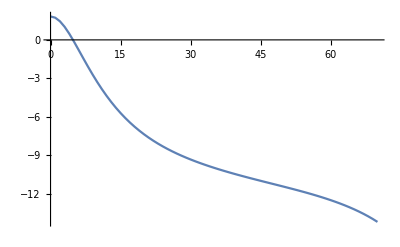

```mathematica
ListPlot[vv, Joined->True]
```

```mathematica
ListPlot[inv, Joined->True]
```

ListPlot::lpn: inv 不是由数字或者数对组成的列表.

ListPlot[inv,Joined→True]

## Step 5 (a). Load plotting program and Data

```mathematica
(*
dav={{{10,-3.8},ErrorBar[0.5]},{{20,-7.2},ErrorBar[0.5]},{{30,-8.8},ErrorBar[0.5]},{{40,-10.0},ErrorBar[0.5]},{{50,-11.2},ErrorBar[0.5]},{{60,-12.1},ErrorBar[0.5]},{{70,-13.8},ErrorBar[0.5]}};

dah={{{10,-3.8},ErrorBar[0.5]},{{20,-7.2},ErrorBar[0.5]},{{30,-8.8},ErrorBar[0.5]},{{40,-10.0},ErrorBar[0.5]},{{50,-11.2},ErrorBar[0.5]},{{60,-12.1},ErrorBar[0.5]},{{70,-13.8},ErrorBar[0.5]}};



g1=Graphics[MultipleListPlot[vv,hh,dav,dah,
	PlotStyle->{Dashing[{0.03,0.03}],Dashing[{0.01,0.01}],{Hue[.85]},{Hue[.3]},{Hue[0.5]},{Hue[0.1]}},
	AspectRatio->1,
	PlotLegend->{FontForm["vv",{"Arial",14}],FontForm["hh",{"Arial",14}],FontForm["dav",{"Arial",14}],FontForm["dah",{"Arial",14}],FontForm["vIEM",{"Arial",14}],FontForm["hIEM",{"Arial",14}]},
	PlotRange->{-15,5},DisplayFunction->Identity,
	SymbolShape->{MakeSymbol[RegularPolygon[5,0]],MakeSymbol[RegularPolygon[4,0]],PlotSymbol[Star,5],PlotSymbol[Diamond,5],MakeSymbol[RegularPolygon[3,0]],MakeSymbol[RegularPolygon[6,0]]},
		PlotLabel->FontForm["Scattering Coefficient",{"Arial",16}],Frame->True,Axes->False,
	PlotJoined->{True,True,False,False,True,True},FrameLabel->{FontForm["θ",{"Arial",18}],FontForm["σ^0",{"Arial",18}]},Background->GrayLevel[0.998],DefaultFont->14,GridLines->Automatic,RotateLabel->False]];*)
```

## Step 6 (a). Show plots (vol 3. p. 1858--short alfalfa and wetter ground)----Fig 8.5 (a)

```mathematica
Show[g1,DisplayFunction->$DisplayFunction];
```

## Step 3 (b). Compute backscattering for alfalfa-tall--drier ground (see p. 2096 for estimating soil er)

```mathematica
fr=13;  al=0.27;tau=2.5; phs=180;
theta=thetas;er=1.2-I 0.01;erb=10.0-I 3; sig1=.15;sig2=0.15; L1=1.5; L2=1.5;sp=1;

start=0.010;end=70.01;step=1;

outp=Table[Rlay[fr,al,tau,theta,thetas,phs,er,erb/er,sig1,sig2,L1,L2,sp],{thetas,start,end,step}];
vv=Map[{#[[1]],#[[2]]}&,outp];
hh=Map[{#[[1]],#[[3]]}&,outp];
vov=Map[{#[[1]],#[[4]]}&,outp];
voh=Map[{#[[1]],#[[5]]}&,outp];
inv=Map[{#[[1]],#[[6]]}&,outp];
inh=Map[{#[[1]],#[[7]]}&,outp];
stv=Map[{#[[1]],#[[8]]}&,outp];
sth=Map[{#[[1]],#[[9]]}&,outp];
sbv=Map[{#[[1]],#[[10]]}&,outp];
sbh=Map[{#[[1]],#[[11]]}&,outp];
cov=Map[{#[[1]],#[[12]]}&,outp];
coh=Map[{#[[1]],#[[13]]}&,outp];

Print[TableForm[{vv,vov,inv,stv,sbv},TableHeadings->{{"VV σ^0"},{"MyLayer"}}]];
(*Print[TableForm[{hh,voh,inh,sth,sbh},TableHeadings->{{"HH σ^0"},{"Layer"}}]];*)
```

| MyLayer |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
VV σ^0 | 0.01
-6.11592 | 1.01
-6.13702 | 2.01
-6.1943 | 3.01
-6.27604 | 4.01
-6.36884 | 5.01
-6.46194 | 6.01
-6.54877 | 7.01
-6.6265 | 8.01
-6.69473 | 9.01
-6.75437 | 10.01
-6.80678 | 11.01
-6.85344 | 12.01
-6.89566 | 13.01
-6.93457 | 14.01
-6.97109 | 15.01
-7.00595 | 16.01
-7.03975 | 17.01
-7.07297 | 18.01
-7.10597 | 19.01
-7.13907 | 20.01
-7.17251 | 21.01
-7.20649 | 22.01
-7.24118 | 23.01
-7.27671 | 24.01
-7.31321 | 25.01
-7.35079 | 26.01
-7.38952 | 27.01
-7.4295 | 28.01
-7.47079 | 29.01
-7.51347 | 30.01
-7.5576 | 31.01
-7.60324 | 32.01
-7.65047 | 33.01
-7.69933 | 34.01
-7.7499 | 35.01
-7.80224 | 36.01
-7.8564 | 37.01
-7.91247 | 38.01
-7.9705 | 39.01
-8.03058 | 40.01
-8.09278 | 41.01
-8.15718 | 42.01
-8.22388 | 43.01
-8.29296 | 44.01
-8.36452 | 45.01
-8.43868 | 46.01
-8.51553 | 47.01
-8.59521 | 48.01
-8.67785 | 49.01
-8.7636 | 50.01
-8.8526 | 51.01
-8.94503 | 52.01
-9.04108 | 53.01
-9.14095 | 54.01
-9.24487 | 55.01
-9.35308 | 56.01
-9.46588 | 57.01
-9.58357 | 58.01
-9.7065 | 59.01
-9.83507 | 60.01
-9.96972 | 61.01
-10.1109 | 62.01
-10.2593 | 63.01
-10.4156 | 64.01
-10.5803 | 65.01
-10.7546 | 66.01
-10.9393 | 67.01
-11.1357 | 68.01
-11.3452 | 69.01
-11.5693 | 70.01
-11.8101
 | 0.01
-6.9832 | 1.01
-6.98384 | 2.01
-6.98575 | 3.01
-6.98893 | 4.01
-6.99338 | 5.01
-6.9991 | 6.01
-7.0061 | 7.01
-7.01438 | 8.01
-7.02395 | 9.01
-7.03481 | 10.01
-7.04697 | 11.01
-7.06045 | 12.01
-7.07525 | 13.01
-7.09138 | 14.01
-7.10885 | 15.01
-7.12768 | 16.01
-7.14788 | 17.01
-7.16947 | 18.01
-7.19246 | 19.01
-7.21687 | 20.01
-7.24272 | 21.01
-7.27003 | 22.01
-7.29883 | 23.01
-7.32912 | 24.01
-7.36095 | 25.01
-7.39433 | 26.01
-7.42929 | 27.01
-7.46587 | 28.01
-7.50409 | 29.01
-7.54399 | 30.01
-7.5856 | 31.01
-7.62896 | 32.01
-7.67412 | 33.01
-7.72111 | 34.01
-7.76998 | 35.01
-7.82078 | 36.01
-7.87356 | 37.01
-7.92837 | 38.01
-7.98529 | 39.01
-8.04436 | 40.01
-8.10566 | 41.01
-8.16926 | 42.01
-8.23524 | 43.01
-8.30368 | 44.01
-8.37467 | 45.01
-8.44832 | 46.01
-8.52473 | 47.01
-8.60402 | 48.01
-8.68631 | 49.01
-8.77174 | 50.01
-8.86046 | 51.01
-8.95264 | 52.01
-9.04846 | 53.01
-9.14812 | 54.01
-9.25185 | 55.01
-9.35989 | 56.01
-9.47252 | 57.01
-9.59005 | 58.01
-9.71283 | 59.01
-9.84124 | 60.01
-9.97574 | 61.01
-10.1168 | 62.01
-10.2651 | 63.01
-10.4211 | 64.01
-10.5858 | 65.01
-10.7599 | 66.01
-10.9444 | 67.01
-11.1406 | 68.01
-11.3499 | 69.01
-11.5739 | 70.01
-11.8145
 | 0.01
-28.8289 | 1.01
-28.8363 | 2.01
-28.858 | 3.01
-28.8942 | 4.01
-28.9449 | 5.01
-29.0102 | 6.01
-29.0902 | 7.01
-29.1851 | 8.01
-29.295 | 9.01
-29.4203 | 10.01
-29.561 | 11.01
-29.7176 | 12.01
-29.8902 | 13.01
-30.0793 | 14.01
-30.2852 | 15.01
-30.5084 | 16.01
-30.7494 | 17.01
-31.0086 | 18.01
-31.2866 | 19.01
-31.5841 | 20.01
-31.9017 | 21.01
-32.2403 | 22.01
-32.6006 | 23.01
-32.9835 | 24.01
-33.3902 | 25.01
-33.8216 | 26.01
-34.2791 | 27.01
-34.764 | 28.01
-35.2778 | 29.01
-35.8223 | 30.01
-36.3995 | 31.01
-37.0114 | 32.01
-37.6606 | 33.01
-38.35 | 34.01
-39.0829 | 35.01
-39.8631 | 36.01
-40.6952 | 37.01
-41.5847 | 38.01
-42.5381 | 39.01
-43.5634 | 40.01
-44.6709 | 41.01
-45.8735 | 42.01
-47.188 | 43.01
-48.6375 | 44.01
-50.2541 | 45.01
-52.0853 | 46.01
-54.2052 | 47.01
-56.7406 | 48.01
-59.9365 | 49.01
-64.376 | 50.01
-72.2051 | 51.01
-83.0521 | 52.01
-69.2643 | 53.01
-64.7661 | 54.01
-62.2391 | 55.01
-60.6164 | 56.01
-59.5251 | 57.01
-58.7909 | 58.01
-58.3183 | 59.01
-58.0497 | 60.01
-57.9476 | 61.01
-57.9866 | 62.01
-58.1486 | 63.01
-58.4204 | 64.01
-58.7922 | 65.01
-59.2564 | 66.01
-59.8069 | 67.01
-60.4392 | 68.01
-61.1492 | 69.01
-61.9337 | 70.01
-62.7898
 | 0.01
-15.8585 | 1.01
-15.9843 | 2.01
-16.3391 | 3.01
-16.8827 | 4.01
-17.5634 | 5.01
-18.3303 | 6.01
-19.1413 | 7.01
-19.9652 | 8.01
-20.7811 | 9.01
-21.576 | 10.01
-22.3427 | 11.01
-23.0776 | 12.01
-23.7796 | 13.01
-24.4487 | 14.01
-25.0862 | 15.01
-25.6933 | 16.01
-26.2718 | 17.01
-26.8232 | 18.01
-27.3492 | 19.01
-27.8512 | 20.01
-28.3309 | 21.01
-28.7894 | 22.01
-29.2281 | 23.01
-29.6482 | 24.01
-30.0507 | 25.01
-30.4366 | 26.01
-30.8069 | 27.01
-31.1625 | 28.01
-31.5041 | 29.01
-31.8326 | 30.01
-32.1486 | 31.01
-32.4529 | 32.01
-32.7461 | 33.01
-33.0289 | 34.01
-33.3017 | 35.01
-33.5653 | 36.01
-33.8202 | 37.01
-34.0669 | 38.01
-34.3059 | 39.01
-34.5378 | 40.01
-34.7631 | 41.01
-34.9822 | 42.01
-35.1958 | 43.01
-35.4043 | 44.01
-35.6081 | 45.01
-35.808 | 46.01
-36.0043 | 47.01
-36.1977 | 48.01
-36.3887 | 49.01
-36.5779 | 50.01
-36.7659 | 51.01
-36.9535 | 52.01
-37.1412 | 53.01
-37.33 | 54.01
-37.5205 | 55.01
-37.7137 | 56.01
-37.9105 | 57.01
-38.112 | 58.01
-38.3192 | 59.01
-38.5334 | 60.01
-38.7561 | 61.01
-38.9886 | 62.01
-39.2328 | 63.01
-39.4903 | 64.01
-39.7633 | 65.01
-40.0538 | 66.01
-40.3644 | 67.01
-40.6975 | 68.01
-41.0557 | 69.01
-41.4415 | 70.01
-41.8572
 | 0.01
-17.6923 | 1.01
-17.7988 | 2.01
-18.1014 | 3.01
-18.5713 | 4.01
-19.1702 | 5.01
-19.8586 | 6.01
-20.6015 | 7.01
-21.3717 | 8.01
-22.1493 | 9.01
-22.9211 | 10.01
-23.6789 | 11.01
-24.418 | 12.01
-25.136 | 13.01
-25.8325 | 14.01
-26.5075 | 15.01
-27.162 | 16.01
-27.7972 | 17.01
-28.4144 | 18.01
-29.015 | 19.01
-29.6004 | 20.01
-30.172 | 21.01
-30.731 | 22.01
-31.2788 | 23.01
-31.8166 | 24.01
-32.3455 | 25.01
-32.8667 | 26.01
-33.3811 | 27.01
-33.8898 | 28.01
-34.3937 | 29.01
-34.8939 | 30.01
-35.3912 | 31.01
-35.8865 | 32.01
-36.3807 | 33.01
-36.8747 | 34.01
-37.3693 | 35.01
-37.8652 | 36.01
-38.3635 | 37.01
-38.8648 | 38.01
-39.37 | 39.01
-39.8799 | 40.01
-40.3953 | 41.01
-40.9171 | 42.01
-41.4461 | 43.01
-41.983 | 44.01
-42.5288 | 45.01
-43.0842 | 46.01
-43.6502 | 47.01
-44.2275 | 48.01
-44.817 | 49.01
-45.4196 | 50.01
-46.0362 | 51.01
-46.6676 | 52.01
-47.3147 | 53.01
-47.9784 | 54.01
-48.6596 | 55.01
-49.3591 | 56.01
-50.0777 | 57.01
-50.8164 | 58.01
-51.576 | 59.01
-52.3572 | 60.01
-53.1608 | 61.01
-53.9876 | 62.01
-54.8381 | 63.01
-55.7131 | 64.01
-56.6131 | 65.01
-57.5385 | 66.01
-58.4898 | 67.01
-59.4672 | 68.01
-60.4711 | 69.01
-61.5015 | 70.01
-62.5586

| MyLayer |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
VV σ^0 | 0.01
-4.52698 | 1.01
-4.52738 | 2.01
-4.52858 | 3.01
-4.53055 | 4.01
-4.53332 | 5.01
-4.53687 | 6.01
-4.54121 | 7.01
-4.54634 | 8.01
-4.55225 | 9.01
-4.55895 | 10.01
-4.56642 | 11.01
-4.57468 | 12.01
-4.58372 | 13.01
-4.59354 | 14.01
-4.60414 | 15.01
-4.61551 | 16.01
-4.62767 | 17.01
-4.64059 | 18.01
-4.6543 | 19.01
-4.66878 | 20.01
-4.68404 | 21.01
-4.70007 | 22.01
-4.71688 | 23.01
-4.73447 | 24.01
-4.75284 | 25.01
-4.77199 | 26.01
-4.79193 | 27.01
-4.81266 | 28.01
-4.83419 | 29.01
-4.85651 | 30.01
-4.87964 | 31.01
-4.90357 | 32.01
-4.92833 | 33.01
-4.95391 | 34.01
-4.98032 | 35.01
-5.00757 | 36.01
-5.03568 | 37.01
-5.06465 | 38.01
-5.0945 | 39.01
-5.12524 | 40.01
-5.15687 | 41.01
-5.18942 | 42.01
-5.2229 | 43.01
-5.25733 | 44.01
-5.29273 | 45.01
-5.3291 | 46.01
-5.36648 | 47.01
-5.40488 | 48.01
-5.44433 | 49.01
-5.48484 | 50.01
-5.52645 | 51.01
-5.56919 | 52.01
-5.61307 | 53.01
-5.65814 | 54.01
-5.70444 | 55.01
-5.75199 | 56.01
-5.80084 | 57.01
-5.85104 | 58.01
-5.90263 | 59.01
-5.95568 | 60.01
-6.01025 | 61.01
-6.0664 | 62.01
-6.12422 | 63.01
-6.18377 | 64.01
-6.24516 | 65.01
-6.30849 | 66.01
-6.37387 | 67.01
-6.44141 | 68.01
-6.51124 | 69.01
-6.58352 | 70.01
-6.65837
 | 0.01
-6.9832 | 1.01
-6.98384 | 2.01
-6.98575 | 3.01
-6.98893 | 4.01
-6.99338 | 5.01
-6.9991 | 6.01
-7.0061 | 7.01
-7.01438 | 8.01
-7.02395 | 9.01
-7.03481 | 10.01
-7.04697 | 11.01
-7.06045 | 12.01
-7.07525 | 13.01
-7.09138 | 14.01
-7.10885 | 15.01
-7.12768 | 16.01
-7.14788 | 17.01
-7.16947 | 18.01
-7.19246 | 19.01
-7.21687 | 20.01
-7.24272 | 21.01
-7.27003 | 22.01
-7.29883 | 23.01
-7.32912 | 24.01
-7.36095 | 25.01
-7.39433 | 26.01
-7.42929 | 27.01
-7.46587 | 28.01
-7.50409 | 29.01
-7.54399 | 30.01
-7.5856 | 31.01
-7.62896 | 32.01
-7.67412 | 33.01
-7.72111 | 34.01
-7.76998 | 35.01
-7.82078 | 36.01
-7.87356 | 37.01
-7.92837 | 38.01
-7.98529 | 39.01
-8.04436 | 40.01
-8.10566 | 41.01
-8.16926 | 42.01
-8.23524 | 43.01
-8.30368 | 44.01
-8.37467 | 45.01
-8.44832 | 46.01
-8.52473 | 47.01
-8.60402 | 48.01
-8.68631 | 49.01
-8.77174 | 50.01
-8.86046 | 51.01
-8.95264 | 52.01
-9.04846 | 53.01
-9.14812 | 54.01
-9.25185 | 55.01
-9.35989 | 56.01
-9.47252 | 57.01
-9.59005 | 58.01
-9.71283 | 59.01
-9.84124 | 60.01
-9.97574 | 61.01
-10.1168 | 62.01
-10.2651 | 63.01
-10.4211 | 64.01
-10.5858 | 65.01
-10.7599 | 66.01
-10.9444 | 67.01
-11.1406 | 68.01
-11.3499 | 69.01
-11.5739 | 70.01
-11.8145
 | 0.01
-28.8289 | 1.01
-28.8363 | 2.01
-28.858 | 3.01
-28.8942 | 4.01
-28.9449 | 5.01
-29.0102 | 6.01
-29.0902 | 7.01
-29.1851 | 8.01
-29.295 | 9.01
-29.4203 | 10.01
-29.561 | 11.01
-29.7176 | 12.01
-29.8902 | 13.01
-30.0793 | 14.01
-30.2852 | 15.01
-30.5084 | 16.01
-30.7494 | 17.01
-31.0086 | 18.01
-31.2866 | 19.01
-31.5841 | 20.01
-31.9017 | 21.01
-32.2403 | 22.01
-32.6006 | 23.01
-32.9835 | 24.01
-33.3902 | 25.01
-33.8216 | 26.01
-34.2791 | 27.01
-34.764 | 28.01
-35.2778 | 29.01
-35.8223 | 30.01
-36.3995 | 31.01
-37.0114 | 32.01
-37.6606 | 33.01
-38.35 | 34.01
-39.0829 | 35.01
-39.8631 | 36.01
-40.6952 | 37.01
-41.5847 | 38.01
-42.5381 | 39.01
-43.5634 | 40.01
-44.6709 | 41.01
-45.8735 | 42.01
-47.188 | 43.01
-48.6375 | 44.01
-50.2541 | 45.01
-52.0853 | 46.01
-54.2052 | 47.01
-56.7406 | 48.01
-59.9365 | 49.01
-64.376 | 50.01
-72.2051 | 51.01
-83.0521 | 52.01
-69.2643 | 53.01
-64.7661 | 54.01
-62.2391 | 55.01
-60.6164 | 56.01
-59.5251 | 57.01
-58.7909 | 58.01
-58.3183 | 59.01
-58.0497 | 60.01
-57.9476 | 61.01
-57.9866 | 62.01
-58.1486 | 63.01
-58.4204 | 64.01
-58.7922 | 65.01
-59.2564 | 66.01
-59.8069 | 67.01
-60.4392 | 68.01
-61.1492 | 69.01
-61.9337 | 70.01
-62.7898
 | 0.01
-8.23909 | 1.01
-8.23909 | 2.01
-8.23909 | 3.01
-8.23909 | 4.01
-8.23909 | 5.01
-8.23909 | 6.01
-8.23909 | 7.01
-8.23909 | 8.01
-8.23909 | 9.01
-8.23909 | 10.01
-8.23909 | 11.01
-8.23909 | 12.01
-8.23909 | 13.01
-8.23909 | 14.01
-8.23909 | 15.01
-8.23909 | 16.01
-8.23909 | 17.01
-8.23909 | 18.01
-8.23909 | 19.01
-8.23909 | 20.01
-8.23909 | 21.01
-8.23909 | 22.01
-8.23909 | 23.01
-8.23909 | 24.01
-8.23909 | 25.01
-8.23909 | 26.01
-8.23909 | 27.01
-8.23909 | 28.01
-8.23909 | 29.01
-8.23909 | 30.01
-8.23909 | 31.01
-8.23909 | 32.01
-8.23909 | 33.01
-8.23909 | 34.01
-8.23909 | 35.01
-8.23909 | 36.01
-8.23909 | 37.01
-8.23909 | 38.01
-8.23909 | 39.01
-8.23909 | 40.01
-8.23909 | 41.01
-8.23909 | 42.01
-8.23909 | 43.01
-8.23909 | 44.01
-8.23909 | 45.01
-8.23909 | 46.01
-8.23909 | 47.01
-8.23909 | 48.01
-8.23909 | 49.01
-8.23909 | 50.01
-8.23909 | 51.01
-8.23909 | 52.01
-8.23909 | 53.01
-8.23909 | 54.01
-8.23909 | 55.01
-8.23909 | 56.01
-8.23909 | 57.01
-8.23909 | 58.01
-8.23909 | 59.01
-8.23909 | 60.01
-8.23909 | 61.01
-8.23909 | 62.01
-8.23909 | 63.01
-8.23909 | 64.01
-8.23909 | 65.01
-8.23909 | 66.01
-8.23909 | 67.01
-8.23909 | 68.01
-8.23909 | 69.01
-8.23909 | 70.01
-8.23909
 | 0.01
-29.9719 | 1.01
-29.9748 | 2.01
-29.9834 | 3.01
-29.9978 | 4.01
-30.0179 | 5.01
-30.0437 | 6.01
-30.0754 | 7.01
-30.1129 | 8.01
-30.1562 | 9.01
-30.2055 | 10.01
-30.2607 | 11.01
-30.322 | 12.01
-30.3893 | 13.01
-30.4629 | 14.01
-30.5427 | 15.01
-30.6289 | 16.01
-30.7215 | 17.01
-30.8207 | 18.01
-30.9266 | 19.01
-31.0392 | 20.01
-31.1588 | 21.01
-31.2855 | 22.01
-31.4194 | 23.01
-31.5607 | 24.01
-31.7095 | 25.01
-31.8661 | 26.01
-32.0306 | 27.01
-32.2032 | 28.01
-32.3842 | 29.01
-32.5737 | 30.01
-32.772 | 31.01
-32.9794 | 32.01
-33.1961 | 33.01
-33.4224 | 34.01
-33.6586 | 35.01
-33.9049 | 36.01
-34.1618 | 37.01
-34.4295 | 38.01
-34.7084 | 39.01
-34.9989 | 40.01
-35.3013 | 41.01
-35.6161 | 42.01
-35.9437 | 43.01
-36.2844 | 44.01
-36.6389 | 45.01
-37.0075 | 46.01
-37.3907 | 47.01
-37.7891 | 48.01
-38.2032 | 49.01
-38.6335 | 50.01
-39.0807 | 51.01
-39.5452 | 52.01
-40.0276 | 53.01
-40.5287 | 54.01
-41.049 | 55.01
-41.5891 | 56.01
-42.1496 | 57.01
-42.7313 | 58.01
-43.3346 | 59.01
-43.9604 | 60.01
-44.6091 | 61.01
-45.2814 | 62.01
-45.9778 | 63.01
-46.6989 | 64.01
-47.4452 | 65.01
-48.2171 | 66.01
-49.0152 | 67.01
-49.8398 | 68.01
-50.6913 | 69.01
-51.57 | 70.01
-52.4762

Check the V-polarized volume-subsurface interaction term

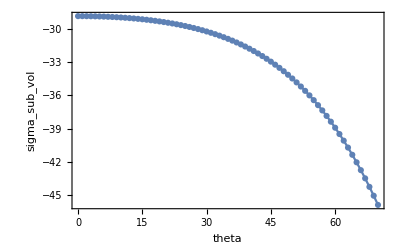

```mathematica
ListPlot[inh, Joined->True, Mesh->All, Frame->True, FrameLabel->{"theta", "sigma_sub_vol"}]
```

## Step 4 (b). Load plotting program and Data

```mathematica
Needs["Statistics`DataManipulation`"];
Needs["Graphics`MultipleListPlot`"];


dav={{{0,-6.},ErrorBar[0.5]},{{10,-7.0},ErrorBar[0.5]},{{20,-7.2},ErrorBar[0.5]},{{30,-7.8},ErrorBar[0.5]},{{40,-7.9},ErrorBar[0.5]},{{50,-9.2},ErrorBar[0.5]},{{60,-10.2},ErrorBar[0.5]},{{70,-12.2},ErrorBar[0.5]}};

dah={{{0,-6.},ErrorBar[0.5]},{{10,-7.0},ErrorBar[0.5]},{{20,-7.2},ErrorBar[0.5]},{{30,-7.8},ErrorBar[0.5]},{{40,-7.9},ErrorBar[0.5]},{{50,-9.2},ErrorBar[0.5]},{{60,-10.2},ErrorBar[0.5]},{{70,-12.2},ErrorBar[0.5]}};

vv

g1=Graphics[MultipleListPlot[vv,hh,dav,dah,
	PlotStyle->{Dashing[{0.03,0.03}],Dashing[{0.01,0.01}],{Hue[.85]},{Hue[.3]},{Hue[0.5]},{Hue[0.1]}},
	AspectRatio->1,
	PlotLegend->{FontForm["vv",{"Arial",14}],FontForm["hh",{"Arial",14}],FontForm["dav",{"Arial",14}],FontForm["dah",{"Arial",14}],FontForm["vIEM",{"Arial",14}],FontForm["hIEM",{"Arial",14}]},
	PlotRange->{-15,-5},DisplayFunction->Identity,
	SymbolShape->{MakeSymbol[RegularPolygon[5,0]],MakeSymbol[RegularPolygon[4,0]],PlotSymbol[Star,5],PlotSymbol[Diamond,5],MakeSymbol[RegularPolygon[3,0]],MakeSymbol[RegularPolygon[6,0]]},
		PlotLabel->FontForm["Scattering Coefficient",{"Arial",16}],Frame->True,Axes->False,
	PlotJoined->{True,True,False,False,True,True},FrameLabel->{FontForm["θ",{"Arial",18}],FontForm["σ^0",{"Arial",18}]},Background->GrayLevel[0.998],DefaultFont->14,GridLines->Automatic,RotateLabel->False]];
```

Get::noopen: 无法打开 Statistics`DataManipulation`.

Needs::nocont: 当运行  Needs 时，没有创建上下文 Statistics`DataManipulation`.

Get::noopen: 无法打开 Graphics`MultipleListPlot`.

Needs::nocont: 当运行  Needs 时，没有创建上下文 Graphics`MultipleListPlot`.

{{0.01,-6.11592},{1.01,-6.13702},{2.01,-6.1943},{3.01,-6.27604},{4.01,-6.36884},{5.01,-6.46194},{6.01,-6.54877},{7.01,-6.6265},{8.01,-6.69473},{9.01,-6.75437},{10.01,-6.80678},{11.01,-6.85344},{12.01,-6.89566},{13.01,-6.93457},{14.01,-6.97109},{15.01,-7.00595},{16.01,-7.03975},{17.01,-7.07297},{18.01,-7.10597},{19.01,-7.13907},{20.01,-7.17251},{21.01,-7.20649},{22.01,-7.24118},{23.01,-7.27671},{24.01,-7.31321},{25.01,-7.35079},{26.01,-7.38952},{27.01,-7.4295},{28.01,-7.47079},{29.01,-7.51347},{30.01,-7.5576},{31.01,-7.60324},{32.01,-7.65047},{33.01,-7.69933},{34.01,-7.7499},{35.01,-7.80224},{36.01,-7.8564},{37.01,-7.91247},{38.01,-7.9705},{39.01,-8.03058},{40.01,-8.09278},{41.01,-8.15718},{42.01,-8.22388},{43.01,-8.29296},{44.01,-8.36452},{45.01,-8.43868},{46.01,-8.51553},{47.01,-8.59521},{48.01,-8.67785},{49.01,-8.7636},{50.01,-8.8526},{51.01,-8.94503},{52.01,-9.04108},{53.01,-9.14095},{54.01,-9.24487},{55.01,-9.35308},{56.01,-9.46588},{57.01,-9.58357},{58.01,-9.7065},{59.01,-9.83507},{60.01,-9.96972},{61.01,-10.1109},{62.01,-10.2593},{63.01,-10.4156},{64.01,-10.5803},{65.01,-10.7546},{66.01,-10.9393},{67.01,-11.1357},{68.01,-11.3452},{69.01,-11.5693},{70.01,-11.8101}}

```mathematica
vv
```

{{0.01,-6.11592},{1.01,-6.13702},{2.01,-6.1943},{3.01,-6.27604},{4.01,-6.36884},{5.01,-6.46194},{6.01,-6.54877},{7.01,-6.6265},{8.01,-6.69473},{9.01,-6.75437},{10.01,-6.80678},{11.01,-6.85344},{12.01,-6.89566},{13.01,-6.93457},{14.01,-6.97109},{15.01,-7.00595},{16.01,-7.03975},{17.01,-7.07297},{18.01,-7.10597},{19.01,-7.13907},{20.01,-7.17251},{21.01,-7.20649},{22.01,-7.24118},{23.01,-7.27671},{24.01,-7.31321},{25.01,-7.35079},{26.01,-7.38952},{27.01,-7.4295},{28.01,-7.47079},{29.01,-7.51347},{30.01,-7.5576},{31.01,-7.60324},{32.01,-7.65047},{33.01,-7.69933},{34.01,-7.7499},{35.01,-7.80224},{36.01,-7.8564},{37.01,-7.91247},{38.01,-7.9705},{39.01,-8.03058},{40.01,-8.09278},{41.01,-8.15718},{42.01,-8.22388},{43.01,-8.29296},{44.01,-8.36452},{45.01,-8.43868},{46.01,-8.51553},{47.01,-8.59521},{48.01,-8.67785},{49.01,-8.7636},{50.01,-8.8526},{51.01,-8.94503},{52.01,-9.04108},{53.01,-9.14095},{54.01,-9.24487},{55.01,-9.35308},{56.01,-9.46588},{57.01,-9.58357},{58.01,-9.7065},{59.01,-9.83507},{60.01,-9.96972},{61.01,-10.1109},{62.01,-10.2593},{63.01,-10.4156},{64.01,-10.5803},{65.01,-10.7546},{66.01,-10.9393},{67.01,-11.1357},{68.01,-11.3452},{69.01,-11.5693},{70.01,-11.8101}}

## Step 5. Show plots (vol 3. p. 1858-alfalfa)------------Fig 8.5 (b)

```mathematica
Show[g1,DisplayFunction->$DisplayFunction];
```

```mathematica
vv
```

{{0.01,-6.11592},{1.01,-6.13702},{2.01,-6.1943},{3.01,-6.27604},{4.01,-6.36884},{5.01,-6.46194},{6.01,-6.54877},{7.01,-6.6265},{8.01,-6.69473},{9.01,-6.75437},{10.01,-6.80678},{11.01,-6.85344},{12.01,-6.89566},{13.01,-6.93457},{14.01,-6.97109},{15.01,-7.00595},{16.01,-7.03975},{17.01,-7.07297},{18.01,-7.10597},{19.01,-7.13907},{20.01,-7.17251},{21.01,-7.20649},{22.01,-7.24118},{23.01,-7.27671},{24.01,-7.31321},{25.01,-7.35079},{26.01,-7.38952},{27.01,-7.4295},{28.01,-7.47079},{29.01,-7.51347},{30.01,-7.5576},{31.01,-7.60324},{32.01,-7.65047},{33.01,-7.69933},{34.01,-7.7499},{35.01,-7.80224},{36.01,-7.8564},{37.01,-7.91247},{38.01,-7.9705},{39.01,-8.03058},{40.01,-8.09278},{41.01,-8.15718},{42.01,-8.22388},{43.01,-8.29296},{44.01,-8.36452},{45.01,-8.43868},{46.01,-8.51553},{47.01,-8.59521},{48.01,-8.67785},{49.01,-8.7636},{50.01,-8.8526},{51.01,-8.94503},{52.01,-9.04108},{53.01,-9.14095},{54.01,-9.24487},{55.01,-9.35308},{56.01,-9.46588},{57.01,-9.58357},{58.01,-9.7065},{59.01,-9.83507},{60.01,-9.96972},{61.01,-10.1109},{62.01,-10.2593},{63.01,-10.4156},{64.01,-10.5803},{65.01,-10.7546},{66.01,-10.9393},{67.01,-11.1357},{68.01,-11.3452},{69.01,-11.5693},{70.01,-11.8101}}